# II. Normal Distribution

KTH/ICT:IX1501 - Statistics
Göran Andersson, goeran@kth.se
ver. 151127

## Section. Implementation and Assessment

The course includes two-three project tasks on a total of 4 hp. Data shall be recorded in writing and orally. They will be given a summary grade in scale A-F. The assessment includes how many project tasks which have been resolved, the quality and the implementation of the written and oral presentation. The first two tasks rating E. If you've been approved at the scheduled examination of these, you can at the end of the course, choose to account for a third project task for a higher grade. In general, excellent performance increases the grade one step.

In this project task you will work in a group of two and solve a mathematical task, write a report (Swedish or English) in Mathematica, write an opposition report (one page) on another goups report and prepare a short oral presentation on your solution to the task (Swedish or English).

Carefully read the following information so that you know which rules apply and what is expected of you.

### Section.Subsection Report

The report should be written in Mathematica and contain

title and authors of the report

email@kth.se

a summary containing the results of resolved parts

separate sections for each part containing e.g.

mathematical formulas and equations

a brief discussion

explanatory diagrams

your conclusions.

separate code section (do not mix code and text with conclusions and results)

The report will normally be uploaded one-two days prior to the examination (see 1.5 below).

### 1.2 Opposition Report

The opposition report (one page) shall contain

title and author of the report that the opposition concerns

name of author and email@kth.se to the authors of the opposition report

positive comments

negative comments

improvement suggestions

The opposition report will normally be uploaded before examination (see 1.5 below).

### Section.Subsection Oral Presentation

You should prepare an oral presentation of your solution to the task. The presentation will be carried out with your own laptop and should not take more than five minutes, effective time. A computer projector will be available at the presentation. Please carefully consider your presentation, what is important, in what order and how it will be illustrated. Practice the presentation in advance and make sure to meet the time frame. One of you in the group (of two) will be selected randomly for the oral presentation and the other part will be selected for questioning.

### Section.Subsection Rules

The task is considered individually and assumes that you have full knowledge of all the material you are presenting. In order to be approved, then you have solved the task and be able to explain the entire task and solution.

To account for the task that you do not have solved is considered cheating. It is also cheating to copy the solution or part of a solution from another. If two solutions are presented as (partially) copies they are rejected both.

If the solution contains parts, e.g. background material, which you do not have produced, you must clearly indicate this and indicate the source.

Suspicion of cheating or misleading can be reported to the Disciplinary Board.

### Section.Subsection Examination

The examination is carried out according to the booking in Daisy 2015-12-09.

Please note that this project should be reported in groups of two students.

Application for examination time is done in Daisy, which opens 2015-12-04T08:00 and closes  2015-12-07T08:00. Booking is done in groups of two students. If you do not have any project companion please advertise in KTH Social under “Projektuppgifter”. You may not register as a single without approval of Haris Celik (harisc@kth.se).

Please notice the closing time in Daisy so the opposition groups can be set up properly.

The report shall be uploaded in KTH Social, before 2015-12-07T15:00. 
Only one report per group. Use the following file name syntax
Lastname1Firstname1_Lastname2Firstname2.nb
No å, ä or ö (remove ^∘ and ^¨) and no accents or special characters. Enter no other information in the file name.

The opposition report shall be uploaded in KTH Social, before 2015-12-08T15:00. 
Only one opposition report per group. Use the same filename syntax as above, but the filename shall contain the names of the respondents (not your names). The name of the uploader will be known by the system.

A printed copy of the report must be submitted at examination. Don’t print the code section.

Notice that the report shall always be uploaded in time even if you cannot attend at the oral presentation. In case of illness, etc., then the oral presentation may be made during project 3. If you are unable to attend, you must in advance inform the teacher (in writing).

If you ignore the oral presentation or the uploading of the report without contacting the teacher (in writing) you will have to wait for the next course for a new project exam.

## Section. Preparations

### Section.Subsection Study

Read the following chapters in the course book (Blom). A • means read carefully and a ◦ means glance through.

4.1-4, 4.5, 4.7

5.1-3, 5.5

5.6

6.1-5, 6.7

7.1-4

Hint: Also study the notebooks from the lectures. These contain Mathematica code on how to handle rvs.

### Section.Subsection Convolution(faltning = summan av oberoende stokastisk variabel)

I det här projekt uppgiften ska vi fokusera på summan av oberoende stokastisk variabel (eller slumpmässig variabel). I vissa fall, är det möjligt att bestämma korrekt sannolikhet distribution. I andra fall måste du förlita dig på approximationen. 

In this project task we will focus on a sum of independent stochastic variables (or random variables, rvs). In some cases, it is possible to determine the correct probability distribution. In other cases you have to rely on approximations.

#### Section.Subsection.Subsubsection Theory for Discrete RVS (Teorin för diskret stokastisk variabel)

Fördelningen av summan av två oberoende diskret stokastisk variabel 𝔰=𝔵+𝔶 kan bestämmas genom följande resonnemang. Om summan 𝔰=s och vi har 𝔵=i då är 𝔶 = s - i. Då 𝔵 och 𝔶 är oberoende och sannolikheten är P(𝔵=i∧𝔶=s-i)=P(𝔵=i)P(𝔶=s-i)=pf_𝔵(i)pf_𝔶(s-i)

The distribution of a sum of two independent discrete rvs 𝔰=𝔵+𝔶 can be determined by the following reasoning. If the sum 𝔰=s and we have 𝔵=i then 𝔶=s-i. Since  𝔵 and  𝔶 are independent the probability is

P(𝔵=i∧𝔶=s-i)=P(𝔵=i)P(𝔶=s-i)=pf_𝔵(i)pf_𝔶(s-i)

Om vi summerar alla möjliga värden för i får vi sannolikheten att 𝔰 = s
P(𝔰=s)=pf_𝔖(s)=∑_(∀i) pf_𝔵(i)pf_𝔶(s-i)=∑_(∀i) pf_𝔵(s-i)pf_𝔶(i)

If we add up all the possible values for i we get the probability of that 𝔰=s

P(𝔰=s)=pf_𝔖(s)=∑_(∀i) pf_𝔵(i)pf_𝔶(s-i)=∑_(∀i) pf_𝔵(s-i)pf_𝔶(i)

Summan kallas för faltning, skrivs ofta med en stjärna som operator:  pf_𝔰(s)=(pf_𝔵⋆pf_𝔶)(s). För att hämta alla värden i summan av indexet bör täckas(åtminstone) alla värden av union och provrymden av 𝔵 och 𝔶, t.ex. i∈{Ω_𝔵∪Ω_𝔶}.

This sum is called the convolution, often written with a star as an operator: pf_𝔰(s)=(pf_𝔵⋆pf_𝔶)(s). In order to retrieve all the values in the sum the index should cover (at least) all values of the union of the sample spaces of 𝔵 and  𝔶, i.e. i∈{Ω_𝔵∪Ω_𝔶}.

Om vi skulle vilja fortsätta med 𝔳=𝔵+𝔶+𝔷 kan vi överväga 𝔳=𝔰+𝔷 och använda konvolution summan för 𝔰+𝔷.
If we would like to continue with 𝔳=𝔵+𝔶+𝔷  we can consider 𝔳=𝔰+𝔷 and use the convolution sum for 𝔰+𝔷.

Nu, antag att alla stokastiska variabler 𝔵_i är oberoende stokastisk variabel(iid) och introducera variabeln n för det nummer av stokastisk variabeln i summan. Vi vill att sannolikhet funktionen 
pf_n(s)=P(∑_(i=1)^n 𝔵_i=s)
Now, assume that all rvs 𝔵_i are independent identical distributed (iid) and introduce a variable n for the number of rvs in the sum. We want to get the probability function

pf_n(s)=P(∑_(i=1)^n 𝔵_i=s)

Ett bekvämt sätt är att göra en rekursiv definition:
pf_n(s)=∑_(∀i) pf_1(s-i)pf_(n-1)(i)
A convenient way here is to make a recursive definition:

pf_n(s)=∑_(∀i) pf_1(s-i)pf_(n-1)(i)

#### Section.Subsection.Subsubsection Discrete Examples

The recurrence above can be programmed (see Functions That Remember Values They Have Found). However, in some cases you can use TransformedDistribution, DiscreteConvolve or ListConvolve.

Notice that when you use discrete distributions in Mathematica the PDF actually means the probability function (pf). This means that PDF[𝒟,x] expresses a probability (not a probability density as in the continuous case).

∑_(x=a+1)^b PDF[𝒟,x]==CDF[𝒟,b]-CDF[𝒟,a]==Probability[a<X≤b,X\[Distributed]𝒟]

Notice also that in the discrete case the pf is a discrete function while the cdf is a (piecewise) continuous function.

Example 1

Here's an example of the sum S=X+Y of two uniformly distributed discrete rvs.

```mathematica
ClearAll["`*"]
```

```mathematica
𝒳=DiscreteUniformDistribution[{3,7}];
𝒴=DiscreteUniformDistribution[{10,15}];
Ω=Union[Range[3,7],Range[10,15]]
```

{3,4,5,6,7,10,11,12,13,14,15}

We can use TransformedDistribution in order to compute the distribution of S=X+Y.

```mathematica
𝒮=TransformedDistribution[X+Y,{X\[Distributed]𝒳,Y\[Distributed]𝒴}];
```

The probability of getting the sum 15 is

```mathematica
PDF[𝒮,15]
```

1/10

We can also compute (pf_X⋆pf_Y)(15).

```mathematica
Sum[PDF[𝒳, i] PDF[𝒴, 15 - i], {i, Ω}]
```

1/10

Calculation by hand:

P(S=15)=n_fav/n_tot=(|{{3,12},{4,11},{5,10}}|)/(5×6)=3/30=1/10

Here a plot of the pf:

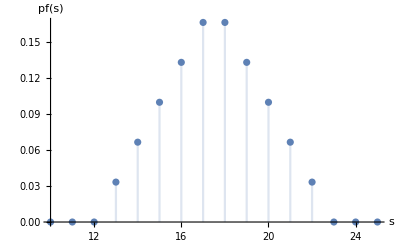

```mathematica
DiscretePlot[Evaluate[PDF[𝒮,s]],{s,10,25},AxesLabel->{HoldForm[s],HoldForm[pf[s]]}]
```

This plot is equivalent to the discrete plot of (pf_X⋆pf_Y)(s). Try to also to plot

Evaluate[
DiscreteConvolve[PDF[𝒳, k], PDF[𝒴, k], k, s]
]

The probability that 15≤S≤18 is

```mathematica
Probability[15≤S≤18,S\[Distributed]𝒮]
```

17/30

Here a plot of the cdf:

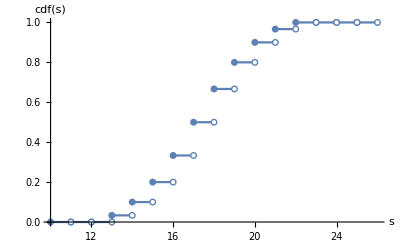

```mathematica
DiscretePlot[Evaluate[CDF[𝒮,s]],{s,10,25},AxesLabel->{HoldForm[s],HoldForm[cdf[s]]},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"},Filling->None]
```

Example 2

```mathematica
ClearAll["`*"]
```

In an amusement park there’s a stand where you can win a giant teddy if you pay €2 and play ten dice. Now, if the sum is 20 or lower or 50 or larger the teddy is yours. What’s the expected value you have to pay for the teddy?

In this case TransformedDistribution is not very efficient. Since the sample space is finite an efficient method is ListConvolve which computes the convolution sum very fast.

```mathematica
P[1]={1/6,1/6,1/6,1/6,1/6,1/6};
P[n_]:=P[n]=ListConvolve[P[n-1],P[1],{1,-1},0]
```

We recognize the probabilities for getting sums 2,3,...,12 if we use two dice:

```mathematica
P[2]
```

{1/36,1/18,1/12,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36}

The probabilities occurs as positions in a list so we can easily make a function of this:

```mathematica
pf[n_,s_]:=P[n]⟦s-n+1⟧
```

The probability of getting the sum 50 in one game is then

```mathematica
pf[10,50]
```

21307/15116544

```mathematica
N[pf[10,50]]
```

0.00140952

The probability of winning the teddy is

```mathematica
Pwin=∑_(s=10)^20 pf[10,s]+∑_(s=50)^60 pf[10,s]
```

87373/15116544

```mathematica
N[Pwin]
```

0.00577996

The number of trials you loose before you win the teddy is geometric distributed. So expected value of the number of games you have to play is

```mathematica
𝒢=GeometricDistribution[Pwin];
Egames=Mean[𝒢]+1
```

15116544/87373

```mathematica
N[%]
```

173.012

```mathematica
N[1/Pwin]
```

173.012

Since you pay €2 for each game the expected value you have to pay for the teddy is around €2×173=€346.

Now if the teddy costs €100, what is the probability that you pay less than this if you roll the dice? Answering this question is equivalent to the problem of computing the probability that the number of losses is less than 49.

```mathematica
N[CDF[𝒢,48]]
```

0.247263

So that’s a fair chance. On the other hand, the probability that you pay at least €100 is around 75% and the probability that you pay at least €200 is

```mathematica
N[1-CDF[𝒢,99]]
```

0.560082

We finish with a plot of the probability function of the sum of ten dice (maybe you recognize the shape).

```mathematica
data=Table[pf[10,s],{s,10,60}]//N
```

{1.65382×10^-8,1.65382×10^-7,9.09599×10^-7,3.6384×10^-6,0.0000118248,0.0000331094,0.0000826082,0.000187543,0.000392947,0.000767702,0.00140952,0.00244666,0.00403407,0.00634189,0.00953533,0.0137466,0.0190416,0.0253868,0.0326237,0.0404573,0.0484644,0.0561241,0.0628704,0.0681581,0.0715327,0.0726928,0.0715327,0.0681581,0.0628704,0.0561241,0.0484644,0.0404573,0.0326237,0.0253868,0.0190416,0.0137466,0.00953533,0.00634189,0.00403407,0.00244666,0.00140952,0.000767702,0.000392947,0.000187543,0.0000826082,0.0000331094,0.0000118248,3.6384×10^-6,9.09599×10^-7,1.65382×10^-7,1.65382×10^-8}

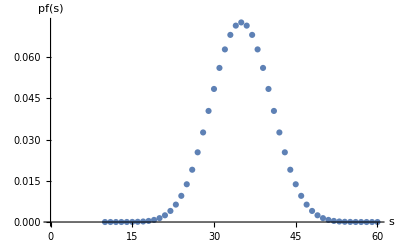

```mathematica
ListPlot[data,DataRange->{10,60},AxesLabel->{HoldForm[s],HoldForm[pf[s]]}]
```

Now, this looks similar to a continuous distribution I’ve seen somewhere.

#### Section.Subsection.Subsubsection Theory for Continuous RVS

The distribution of a sum of two independent continuous rvs 𝔰=𝔵+𝔶 can be determined by the following reasoning. If the sum 𝔰=s and we have 𝔵=t then 𝔶=s-t. Since  𝔵 and  𝔶 are independent the pdf is

pdf_𝔵(i)pdf_𝔶(s-t)

If we integrate over all the possible values of t, where the product is nonzero, we get the probability density at 𝔰=s

pdf_𝔰(s)=∫_(∀t) pdf_𝔵(t)pdf_𝔶(s-t)dt=∫_(∀t) pdf_𝔵(s-t)pdf_𝔶(t)dt

This integral is called convolution, often written with a star pdf_𝔰(s)=(pdf_𝔵⋆pdf_𝔶)(s). In order to retrieve all the values in the integral the variable t should cover (at least) all values of the union of the sample spaces of 𝔵 and  𝔶, i.e. t∈{Ω_𝔵∪Ω_𝔶}.

If we would like to continue with 𝔳=𝔵+𝔶+𝔷  we can consider 𝔳=𝔰+𝔷 and use the convolution sum for 𝔰+𝔷.

Now, assume that all rvs 𝔵_i are iid and introduce a variable n for the number of rvs in the sum. A convenient way here is to make a recursive definition:

pdf_n(s)=∫_(∀t) pdf_1(s-t)pdf_(n-1)(t)dt

#### Section.Subsection.Subsubsection Continuous Examples

The recurrence above can be programmed (see Functions That Remember Values They Have Found). However, in some cases you can use TransformedDistribution or Convolve.

Notice that when you use continuous distributions in Mathematica the PDF means the probability density function. This means that PDF[𝒟,x] has to be integrated over some interval in order to express a probability. The CDF (cumulative distribution function) however, expresses probability.

∫_a^b PDF[𝒟,x]ⅆx==CDF[𝒟,b]-CDF[𝒟,a]==Probability[a<X≤b,X\[Distributed]𝒟]

Example 1

Here's an example of the sum of two uniformly distributed rvs.

```mathematica
ClearAll["`*"]
```

```mathematica
𝒳=UniformDistribution[{3,7}];
𝒴=UniformDistribution[{10,15}];
```

We can use TransformedDistribution in order to compute the distribution of S=X+Y.

```mathematica
𝒮=TransformedDistribution[X+Y,{X\[Distributed]𝒳,Y\[Distributed]𝒴}];
```

The density at 15 is

```mathematica
PDF[𝒮,15]
```

1/10

We can also compute (pdf_X⋆pdf_Y)(15).

```mathematica
Integrate[PDF[𝒳, t] PDF[𝒴, 15 -t], {t,3,7}]+Integrate[PDF[𝒳, t] PDF[𝒴, 15 -t], {t,10,15}]
```

1/10

The pdf is

```mathematica
PDF[𝒮,s]
```

Piecewise[{{1/5, 17<s≤18}, {(22-s)/20, 18<s<22}, {1/20 (-13+s), 13<s≤17}, {0, True}}]

Here a plot of the pdf:

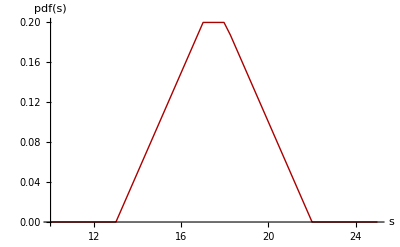

```mathematica
Plot[Evaluate[PDF[𝒮,s]],{s,10,25},AxesLabel->{HoldForm[s],HoldForm[pdf[s]]},PlotStyle->Directive[Darker[Red],Thick],Exclusions->None]
```

Try also to plot

Evaluate[
Convolve[PDF[𝒳,t],PDF[𝒴,t],t,s]
]

The probability that 12<S≤18 is

```mathematica
Probability[12<S≤18,S\[Distributed]𝒮]
```

3/5

```mathematica
CDF[𝒮,18]-CDF[𝒮,12]
```

3/5

Here a plot of the cdf:

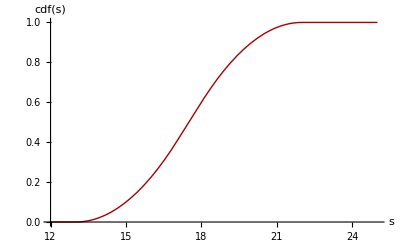

```mathematica
Plot[Evaluate[CDF[𝒮,s]],{s,12,25},AxesLabel->{HoldForm[s],HoldForm[cdf[s]]},PlotStyle->Directive[Darker[Red],Thick],Exclusions->None]
```

Example 2

```mathematica
ClearAll["`*"]
```

Assume that we consider the sum of 10 independent uniform rvs in the interval [0,5]. How does the distribution look like?

We start with one random variable:

```mathematica
𝒟1=UniformDistribution[{0,5}];
```

```mathematica
PDF[𝒟1,t]
```

Piecewise[{{1/5, 0≤t≤5}, {0, True}}]

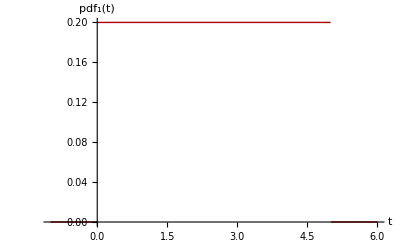

```mathematica
p1=Plot[PDF[𝒟1,t],{t,-1,6},AxesLabel->{HoldForm[t],HoldForm[Subscript[pdf, 1][t]]},PlotStyle->Directive[Darker[Red],Thick]]
```

Looking at the sum of n independent rvs ∑_(i=1)^n X_i where X_i\[Distributed]U(0,5) there is a built-in distribution: UniformSumDistribution.

```mathematica
𝒟[n_]:=UniformSumDistribution[n,{0,5}]
```

```mathematica
PDF[𝒟[2],t]
```

Piecewise[{{0, t<0}, {t/25, 0≤t<5}, {(10-t)/25, 5≤t≤10}, {0, True}}]

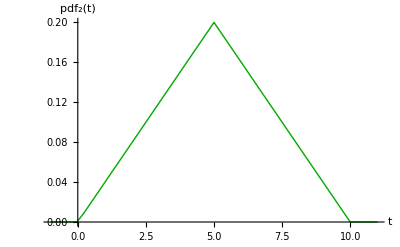

```mathematica
p2=Plot[Evaluate[PDF[𝒟[2],t]],{t,-1,11},AxesLabel->{HoldForm[t],HoldForm[Subscript[pdf, 2][t]]},PlotStyle->Directive[Darker[Green],Thick],Exclusions->None]
```

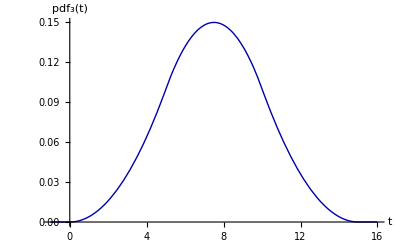

```mathematica
p3=Plot[Evaluate[PDF[𝒟[3],t]],{t,-1,16},AxesLabel->{HoldForm[t],HoldForm[Subscript[pdf, 3][t]]},PlotStyle->Directive[Darker[Blue],Thick],Exclusions->None]
```

And finally the plot of the pdf of ten independent uniform rvs  (maybe you recognize the shape).

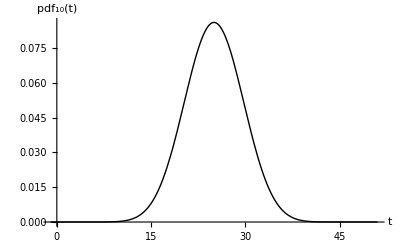

```mathematica
p10=Plot[Evaluate[PDF[𝒟[10],t]],{t,-1,51},AxesLabel->{HoldForm[t],HoldForm[Subscript[pdf, 10][t]]},PlotStyle->Directive[Black,Thick],Exclusions->None]
```

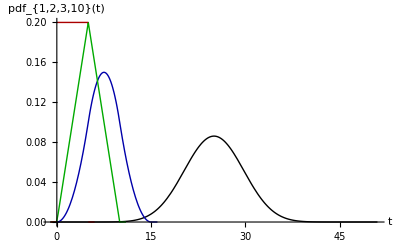

```mathematica
Show[p10,p3,p2,p1,PlotRange->All,AxesLabel->{HoldForm[t],HoldForm[Subscript[pdf, {1,2,3,10}][t]]}]
```

Now, the black function looks similar to a distribution I’ve seen somewhere.

### Section.Subsection Normal Distribution

#### Section.Subsection.Subsubsection Theory

According to the Central Limit Theorem (CLT) a sum 𝔰 of independent rvs 𝔵_i approaches the normal distribution when the number n of variables increases.

∑_(i=1)^n 𝔵_i=𝔰(\[Distributed])^CLT N(μ,σ), μ=∑_(i=1)^n E[𝔵_i], σ^2=^(indep.)∑_(i=1)^n V[𝔵_i]

The average 𝔵̄ satisfies

1/n∑_(i=1)^n 𝔵_i=𝔵̄(\[Distributed])^CLT N(μ,σ), μ=1/n∑_(i=1)^n E[𝔵_i], σ^2=^(indep.)1/n^2∑_(i=1)^n V[𝔵_i]

If all 𝔵_i are iid (independent identical distributed) with μ=E[𝔵_i] and σ^2=V[𝔵_i] we can write

∑_(i=1)^n 𝔵_i==𝔰(\[Distributed])^CLT N(n μ,√n σ)

1/n∑_(i=1)^n 𝔵_i==𝔵̄(\[Distributed])^CLT N(μ,σ/(√n))

#### Section.Subsection.Subsubsection Example

Example: Assume that we consider waiting times at a bus station τ_i\[Distributed]U(0,10) minutes. If we compute the average waiting time τ for 20 persons. What is the error in computing P(τ>6) if we use normal distribution as an approximation?

We can compute the approximate probability with

μ=E[τ_i]=(10-0)/2=5 (*Hittar medianen summan av två värden dividerat med antalet värden*)

σ^2= V[τ_i]=(10-0)^2/12=25/3 (*Variansen är Standard Avvikelsen i kvadrat*)

∴τ=1/20∑_(i=1)^20 τ_i=τ(\[Distributed])^CLT N(5,(√(25/3))/(√20))=N(5, √(5/12)) (*Summerar från i=1 till 20*)

P(τ>6)=1-cdf(6)=1-Φ((6-5)/(√(5/12)))≈1-Φ(1.55)≈0.061

The probability is approximated with 6.1%.

Here's the calculation with Mathematica:

```mathematica
ClearAll["`*"]
```

```mathematica
𝒰=UniformDistribution[{0,10}];
```

```mathematica
μ=Mean[𝒰]
```

5

```mathematica
σ=StandardDeviation[𝒰]
```

5/(√3)

```mathematica
𝒩=NormalDistribution[μ,σ/(√20)];
```

```mathematica
N[Papprox=1-CDF[𝒩,6]]
```

0.0606676

In order to compute the error we need the exact distribution, which is

```mathematica
𝒮=UniformSumDistribution[20,{0,10}/20];
```

We use the UniformSumDistribution for 20 rvs and scale each variable to the interval [0,1/2].

```mathematica
N[Pexact=1-CDF[𝒮,6]]
```

0.0609562

The absolute error is then

```mathematica
absoluteError=N[Papprox-Pexact]
```

-0.000288601

So the absolute error is in this case 0.029pp (percentage points). The relative error is

```mathematica
relativeError=absoluteError/Pexact
```

-0.00473456

I.e. the relative error is 4.7‰.

We finish with a graphical comparison between the exact distribution and the normal approximation:

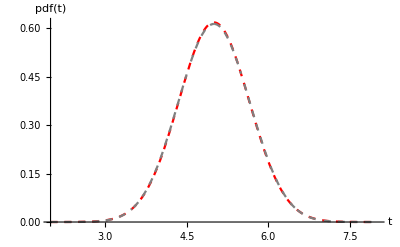

```mathematica
Plot[{PDF[𝒩,t],PDF[𝒮,t]},{t,2,8},PlotStyle->{{Dashed,Red},{Dashed,Gray}},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}]
```

## Section. Mathematical Task

Required for grade E (approved). Keep in mind that it is the mathematical method on the task that is interesting to consider, not the answer. Furthermore, solve the given task, not a variant or extension. A very good report and presentation is graded D.

### The Relative Error of Normal Approximation

If you consider the average(mean(median)) of 20 iid(oberoende stokastisk variabel) rvs(random variabels), normal distribution(normal fördelning) is often considered as a good approximation(approximation to what?). However in this task you will go beyond this recommendation and study under what circumstances it is valid. The exponential distribution is very skew compared to the uniform distribution. How is this effecting the approximation with normal distribution?

In a certain cellular phone system new calls arrives with exponential distributed interarrivaltimes with expectation value μ=λ^-1=3 minutes. The interarrivaltime is the time between two incoming calls.

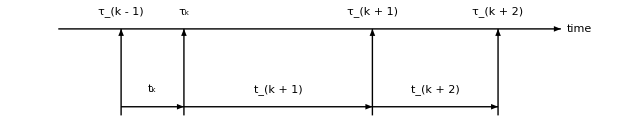

#### Task

Study the average t̄=1/n ∑_(k=1)^n t_k of n=20 interarrival times. Plot the absolute error of the pdf_(t̄)(t) and the cdf_(t̄)(t) using the normal approximation. Make also a plot of the relative error of

P(t̄>x), μ-2σ/√n<x<μ+2σ/√n

Conclusion? Is the approximation always useful?

Hint: The sum of iid exponential rvs has a well-known distribution, which is built-in in Mathematica, ErlangDistribution[n,λ] or GammaDistribution[n,1/λ].

Study the number of incoming calls during one hour. Plot the absolute and relative error of the probability function using normal approximation. Conclusion?

Hint: What is the distribution of the number of events in a certain time interval, e.g 1h, if the time between the events is exponential?

http://math.stackexchange.com/questions/466927/independent-identically-distributed-iid-random-variables